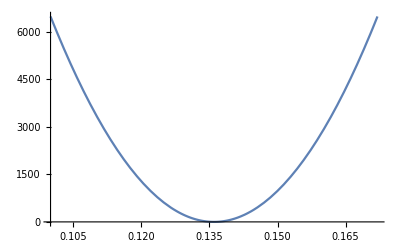

```mathematica
v[x_]:=1/2*k*(x-x0)^2;
parameters={k->1*10^7,kB->0.0083,x0->0.136};Plot[v[x]/.parameters,{x,0.1,0.172}]
```

# Metropolis Monte Carlo

MC: <Epot> = 1.25812 and 0.5 kBT = 1.245

average displacement: 3.67851×10^-6

deviation: 0.000501608

acceptance ratio: 12569/20000

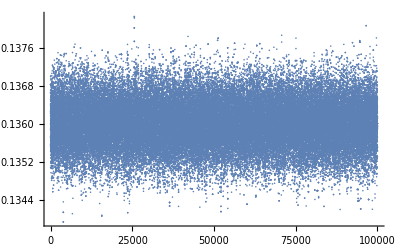

```mathematica
o=0.136;
delta = 0.001;
etot=0;
xav=0;
xavsq=0;
maxsteps=100000;
T=300;
k=1*10^7;
kB=0.0083;
x0=0.136;
nacc=0;
pos=ConstantArray[0,maxsteps];
For[i=1,i≤maxsteps,i++,{
n=o+RandomReal [{-1,1}]*delta;
p=Exp[-1/(T*kB)*(v[n]-v[o])];
rnr=RandomReal[1];
If[p>rnr,{o=n;nacc++}];
};
etot+=v[o];
pos[[i]]=o;
xav+=o-x0;
xavsq+=(o-x0)*(o-x0);
];
Print ["MC: <Epot> = ", etot/maxsteps," and 0.5 kBT = ",1/2*kB*T]
Print ["average displacement: ",xav/maxsteps];
Print["deviation: ",Sqrt[xavsq/maxsteps-(xav/maxsteps)^2]];
Print["acceptance ratio: ",nacc/maxsteps];
ListPlot[pos,PlotRange->All]
Histogram[pos]
```

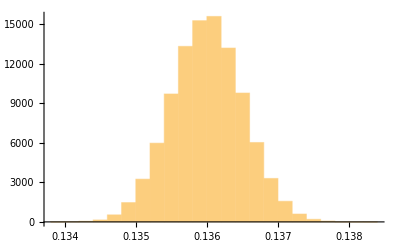

```mathematica
Histogram[pos]
```

```mathematica
Print["accept, p = ",p," RNR = ",rnr]
```

```mathematica
Clear[x];D[v[x],x]
```

10000000 (-0.136+x)

```mathematica
?Histogram
```

Histogram[{x_1,x_2,…}] plots a histogram of the values x_i.
Histogram[{x_1,x_2,…},bspec] plots a histogram with bin width specification bspec.
Histogram[{x_1,x_2,…},bspec,hspec] plots a histogram with bin heights computed according to the specification hspec.
Histogram[{data_1,data_2,…},…] plots histograms for multiple datasets data_i.